# -Graphics-

# Wolfram 语言编程：概念到应用

## 自定义函数

-Graphics-

## 学习目标

定义一个简单的自定义函数

从自定义函数返回的表达式

自定义函数的作用域

重载定义

定义选项和可选参数

记忆化以提高计算效率

自定义函数的属性

各种错误处理技巧，包括消息

OwnValues、DownValues 和 UpValues；UpValues 的用法

DumpSave 和用于存储多个函数的软件包

## 内置函数

Mathematica 包含大量内置函数.

### 内置函数的特点

#### 选项

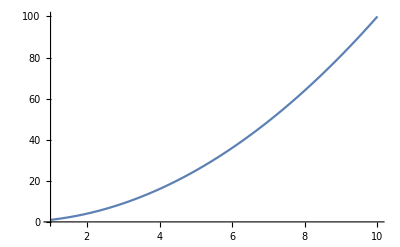
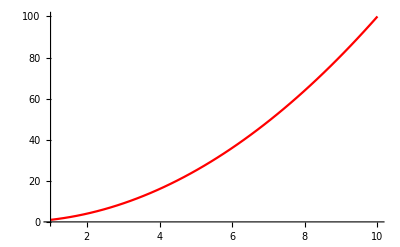

```mathematica
{Plot[x^2,{x,1,10}],Plot[x^2,{x,1,10},PlotStyle->Red]}
```

#### 可选参数

```mathematica
Cases[{1,2,5.0,10.0,{100,200}},_Integer]
Cases[{1,2,5.0,10.0,{100,200}},_Integer,{2}]
```

{1,2}

{100,200}

#### 警告/错误信息

```mathematica
NIntegrate[Cos[20000x]/(√x),{x,0,1}]
```

NIntegrate::ncvb: 在接近 {x} = {0.} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00579916 和 0.0148755.

0.00579916

#### 语法着色

```mathematica
Sin[1,2]
```

Sin::argx: 调用 Sin 时使用了 2 个参数；应该用 1 个参数.

Sin[1,2]

#### 属性

```mathematica
Attributes[Plus]
Attributes[Plot]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

{HoldAll,Protected,ReadProtected}

```mathematica
Sin[{1.,2.,3.}] (* 自动作用于列表属性将函数定义映射到列表 *)
```

{0.841471,0.909297,0.14112}

您可以使用此类特征构建自定义函数.

## 函数定义

可以使用模式和 SetDelayed 定义函数.

简单定义：

```mathematica
fun[x_,y_]:=x^2+y^2
```

```mathematica
fun[3,4]
```

25

#### 检查定义

```mathematica
Definition[fun]
```

fun[x_,y_]:=x^2+y^2

```mathematica
?fun
```

```mathematica
DownValues[fun]
```

{HoldPattern[fun[x_,y_]]:>x^2+y^2}

## 函数定义（续）

#### 命名自定义函数

应使用首字母为小写的驼峰式大小写. 应给出有意义的名称：

```mathematica
findArea[length_,breadth_]:=length*breadth
```

```mathematica
squareANumber[x_]:=x^2
```

#### 返回值

默认情况下，返回最后一个表达式的值：

```mathematica
ClearAll[f]
f[x_,y_]:=(sum=x+y;product=x y;quotient=x/y)
```

```mathematica
f[12,2] (* 商被返回 *)
```

6

```mathematica
{sum,product,quotient} (* 也计算了其他的表达式*)
```

Return 可用于返回中间表达式：

```mathematica
ClearAll[g, sum, product, quotient]
g[x_,y_]:=(sum=x+y;product=x y;Return[product];quotient=x/y)
```

```mathematica
g[12,2] (* 积被返回 *)
```

24

```mathematica
ClearAll[fun,.08x,y]
```

## 作用域

Set 与 SetDelayed

与 Set 不同，SetDelayed 将界定变量：

```mathematica
ClearAll[fun,x,y]
x=5;y=10;
fun[x_,y_]=x^2+y^2
```

125

```mathematica
{fun[1,2],fun[2,3],fun[3,4]}
```

{125,125,125}

```mathematica
ClearAll[fun,x,y]
x=5;y=10;
fun[x_,y_]:=x^2+y^2
```

```mathematica
{fun[1,2],fun[2,3],fun[3,4]}
```

{5,13,25}

Module、Block 和 With

```mathematica
ClearAll[fun]
fun[x_]:=Module[{a=10},x*a]
```

```mathematica
fun[5]
```

50

```mathematica
ClearAll[fun]
fun[x_]:=Block[{$MinPrecision=10,$MaxPrecision=10},x*10]
```

```mathematica
fun[2.3`20]
Precision[%]
```

23.

10.

```mathematica
ClearAll[fun]
fun[x_]:=With[{a=10},x^2+a^2]
```

```mathematica
fun[5]
```

## 函数重载

可以为单个符号分配多个定义.

#### 例子1

```mathematica
ClearAll[evenOddFun]
evenOddFun[x_?EvenQ]:=x/2
evenOddFun[x_?OddQ]:=(x+1)/2
```

```mathematica
evenOddFun[10]
```

5

```mathematica
evenOddFun[11]
```

6

#### 例子2

```mathematica
ClearAll[myAbs]
myAbs[x_/;x>0]:=x
myAbs[x_/;x<0]:=-x
```

```mathematica
myAbs[10]
```

10

```mathematica
myAbs[-10]
```

10

## 定义顺序

对于具有多个定义的自定义函数，在进入通用定义之前，Wolfram 语言™将检查更具体的定义.

计算数字的阶乘：

```mathematica
ClearAll[fact];
fact[n_]:=n fact[n-1]
fact[0]:=1
fact[1]:=1
```

检查定义的存储顺序：

```mathematica
?fact
```

如图所示，Wolfram 语言将在执行更普遍的定义 fact[n_]之前先检查特殊情况 fact[0] 和 fact[1]：

```mathematica
fact[0] (* fact[0] definition is used *)
```

1

```mathematica
fact[1] (* fact[1] definition is used *)
```

1

```mathematica
fact[5] (* fact[n_] definition is used *)
```

120

如果没有足够通用的定义，Wolfram语言将按照用户提供的顺序存储定义：

```mathematica
ClearAll[evenOddFun]
evenOddFun[x_?EvenQ]:=x/2
evenOddFun[x_?OddQ]:=(x+1)/2
```

```mathematica
DownValues[evenOddFun]
```

{HoldPattern[evenOddFun[x_?EvenQ]]:>x/2,HoldPattern[evenOddFun[x_?OddQ]]:>(x+1)/2}

```mathematica
?evenOddFun
(* EvenQ 在 OddQ 之前被触发 *)
```

```mathematica
ClearAll[evenOddFun]
evenOddFun[x_?OddQ]:=(x+1)/2
evenOddFun[x_?EvenQ]:=x/2
```

```mathematica
DownValues[evenOddFun]
```

{HoldPattern[evenOddFun[x_?OddQ]]:>(x+1)/2,HoldPattern[evenOddFun[x_?EvenQ]]:>x/2}

```mathematica
?evenOddFun
(* OddQ 在 EvenQ 之前被触发 *)
```

```mathematica
ClearAll["Global`*"]
```

## 应用——代码管理

重载使函数定义变得整洁且易于管理.

#### 例子1

重载：

```mathematica
ClearAll[factOl];
factOl[n_]:=n factOl[n-1]
factOl[0]:=1
factOl[1]:=1
```

```mathematica
factOl[5]
```

120

使用 If：

```mathematica
ClearAll[factIf];
factIf[n_]:=If[n==1||n==0,1,n factIf[n-1]]
```

```mathematica
factIf[5]
```

120

#### 例子2

用于创建色板的自定义函数：

```mathematica
Clear[rgb]
rgb[r_,g_,b_]:=RGBColor[r,g,b]
```

```mathematica
rgb[1,0,0]
```

```mathematica
rgb[{{0,1,1},{1,0,1}}]
```

使之适用于嵌套列表：
{{1,0,0},{0,1,0}...}

重载：

```mathematica
Clear[rgbOl]
rgbOl[r_,g_,b_]:=RGBColor[r,g,b]
rgbOl[l_List]:=rgbOl@@@l
```

```mathematica
rgbOl[RandomReal[1,{10,3}]]
```

使用 If:

```mathematica
Clear[rgbIf]
rgbIf[x__]:=Module[{l={x}},
If[TrueQ[Head[l[[1]]]==List],
RGBColor@@@x,
RGBColor[l]
]]
```

```mathematica
rgbIf[RandomReal[1,{10,3}]]
```

## 应用——加快计算速度

考虑以下两种定义相同函数的方法：

```mathematica
ClearAll[funcO]
funcO[x_/;x≥0]:=Sqrt[x]
funcO[x_/;x<0]:=Power[x,2]
```

```mathematica
?funcO
```

```mathematica
ClearAll[funcIf]
funcIf[x_]:=If[x≥0,Sqrt[x],Power[x]]
```

对于正数，funcO 更快：

```mathematica
(funcO/@RandomReal[{0,500},10^6]);//AbsoluteTiming
```

{1.05587,Null}

```mathematica
(funcIf/@RandomReal[{0,500},10^6]);//AbsoluteTiming
```

{1.38481,Null}

对于负数，funcO 较慢：

```mathematica
(funcO/@RandomReal[{-500,0},10^6]);//AbsoluteTiming
```

{1.64691,Null}

```mathematica
(funcIf/@RandomReal[{-500,0},10^6]);//AbsoluteTiming
```

{1.28132,Null}

```mathematica
ClearAll["Global`*"]
```

## 选项

定义自定义函数的 Options：

```mathematica
Clear[fn]
Options[fn]={opt1->1,opt2->2}
```

{opt1→1,opt2→2}

使用 OptionsPattern 定义函数：

```mathematica
fn[x_,OptionsPattern[]]:={x,OptionValue[opt1],OptionValue[opt2]}
```

```mathematica
fn[4]
```

{4,1,2}

```mathematica
fn[4,opt1->10,opt2->20]
```

{4,10,20}

可以使用 RuleDelayed：

```mathematica
Clear[fn]
Options[fn]={opt1:>RandomInteger[10],opt2:>RandomInteger[10]};
```

```mathematica
fn[x_,OptionsPattern[]]:={x,OptionValue[opt1],OptionValue[opt2]}
```

```mathematica
{fn[100],fn[100],fn[100]}
```

{{100,10,0},{100,1,8},{100,0,9}}

内置函数的选项也存储在 Options[<function>]中：

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## 选项：FilterRules

在编写包含内置函数的自定义函数时，FilterRules 可能会有所帮助。

根据第二个参数过滤给定的规则：

```mathematica
FilterRules[{x->1,b->2,y->3},{a,b,c}]
```

{b→2}

```mathematica
FilterRules[{ Method->"ExplicitRungeKutta", PlotStyle->Red},Options[NDSolve]]
```

{Method→ExplicitRungeKutta}

函数示例 (tutorial/SettingUpFunctionsWithOptionalArguments#24519065):

```mathematica
odePlot[de_, y_, {x_, x0_, x1_}, opts:OptionsPattern[]] := 
Module[{sol},
sol = NDSolve[de, y, {x,x0,x1},FilterRules[{opts}, Options[NDSolve]]];
If[Head[sol] === NDSolve,
$Failed,
Plot[Evaluate[y /. sol],{x,x0,x1},Evaluate[FilterRules[{opts}, Options[Plot]]]]
]
] (* accepts options that passes to other functions inside *)
```

NDSolve 和 Plot 的默认选项：

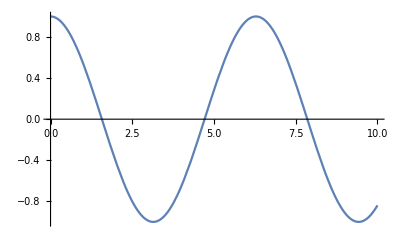

```mathematica
odePlot[{y''[x] + y[x] == 0, y[0] == 1, y'[0] == 0}, y[x], {x,0,10}]
```

odePlot 中指定的选项：

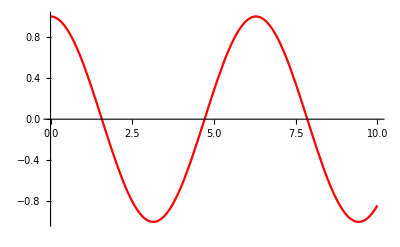

```mathematica
odePlot[{y''[x] + y[x] == 0, y[0] == 1, y'[0] == 0}, y[x], {x,0,10}, Method->"ExplicitRungeKutta", PlotStyle->Red]
```

## 可选参数

函数可以具有默认值的可选参数。

#### 例子1

```mathematica
ClearAll[newFun]
newFun[x_,y_,k_:5]:=x*y*k (* k 是可选参数 *)
```

```mathematica
newFun[10,20,10]
```

2000

```mathematica
newFun[10,20]
```

1000

#### 例子2

```mathematica
ClearAll[newFun2]
newFun2[k1_:5,k2_:10]:=k1+k2 (* k1 和 k2 都是可选参数 *)
```

```mathematica
newFun2[100,200]
```

300

```mathematica
newFun2[]
```

15

## 记忆化

记忆化是指一种技巧，通过该技巧可以存储先前计算的结果并重新使用以加快总体计算速度.

#### 例子1

下面显示了一个传统定义——每次计算 f[5,5,5,5,5]，使用的时间是相同的：

```mathematica
ClearAll[fOrd]
fOrd[a1_,a2_,a3_,a4_,a5_]:=NIntegrate[1/√(x1+x2+x3+x4+x5),{x1,0,a1},{x2,0,a2},{x3,0,a3},{x4,0,a4},{x5,0,a5}]
```

```mathematica
fOrd[5,5,5,5,5]//AbsoluteTiming
```

{0.271752,910.019}

```mathematica
fOrd[5,5,5,5,5]//AbsoluteTiming
```

{0.263811,910.019}

```mathematica
fOrd[5,5,5,5,5]//AbsoluteTiming
```

{0.258246,910.019}

下面显示了一个包含记忆的定义——由于 f[5,5,5,5,5] 存储在定义本身中（作为下值），因此后续计算要快得多：

```mathematica
fMemo[a1_,a2_,a3_,a4_,a5_]:=fMemo[a1,a2,a3,a4,a5]=
NIntegrate[1/√(x1+x2+x3+x4+x5),{x1,0,a1},{x2,0,a2},{x3,0,a3},{x4,0,a4},{x5,0,a5}]
```

```mathematica
fMemo[5,5,5,5,5]//AbsoluteTiming
```

{0.270878,910.019}

```mathematica
fMemo[5,5,5,5,5]//AbsoluteTiming
```

{1.×10^-6,910.019}

```mathematica
fMemo[5,5,5,5,5]//AbsoluteTiming
```

{2.×10^-6,910.019}

#### 例子2

与示例1相同的函数：

```mathematica
fOrd[5,5,5,5,#]&/@RandomInteger[{10,15},50];//AbsoluteTiming
```

{12.0488,Null}

包含记忆的定义：

```mathematica
fMemo[5,5,5,5,#]&/@RandomInteger[{10,15},50];//AbsoluteTiming
```

{1.33627,Null}

#### 例子3

普通定义：

```mathematica
ClearAll[fibOrd]
fibOrd[0]:=1
fibOrd[1]:=1
fibOrd[x_]:=fibOrd[x-1]+fibOrd[x-2]
```

```mathematica
fibOrd[30]//AbsoluteTiming
```

{1.97527,1346269}

包含记忆的定义：

```mathematica
ClearAll[fibMemo]
fibMemo[0]:=1
fibMemo[1]:=1
fibMemo[x_]:=fibMemo[x]=fibMemo[x-1]+fibMemo[x-2]
```

```mathematica
fibMemo[30]//AbsoluteTiming
```

## 属性

自定义函数可以具有以下属性：

```mathematica
CellPrint[ExpressionCell[Grid[{
{"Attributes[f]","显示 f 的属性"},
{"SetAttributes[f, attr]","将 attr 添加到 f 的属性列表"},
{"ClearAttributes[f, attr]","将 attr 从 f 的属性列表中清除"}
},
Alignment->Left,BaseStyle->{FontFamily->"Times",FontColor->GrayLevel[0.15],FontSize->14},
Frame->True,
Background->RGBColor[1,1,0.85],
Spacings->{4,0.8}],"Output",GeneratedCell->False]]
```

Attributes[f] | 显示 f 的属性
SetAttributes[f, attr] | 将 attr 添加到 f 的属性列表
ClearAttributes[f, attr] | 将 attr 从 f 的属性列表中清除

Listable:

```mathematica
ClearAll[f]
f[x_]:=If[x>0,Sqrt[x],Sqrt[-x]];
SetAttributes[f,Listable];
```

```mathematica
f[{4,-4,9,-9}]
```

{2,2,3,3}

HoldAll:

```mathematica
ClearAll[f,a,b,c]
a=5;
b=10;
c=15;
SetAttributes[f,HoldAll]
f[a,b,c]
```

f[a,b,c]

```mathematica
ClearAll[f,a,b,c]
a=5;
b=10;
c=15;
f[a,b,c]
```

```mathematica
ClearAll[f]
```

#### 所有支持的属性列表

Wolfram语言 提供了一些属性，可用于指定函数的各种属性.（这将在第5课——计算控制中进一步讨论.）

-Graphics-

## 错误处理：类型检查

一个简单的函数定义：

```mathematica
f[x_,y_]:=x^2+y^2
```

```mathematica
f[5,10]
```

125

如果输入数字以外的参数时会遇到问题：

```mathematica
f["hello","today"]
```

hello^2+today^2

因此，类型检查很重要：

```mathematica
ClearAll[f]
f[x_?NumberQ,y_?NumberQ]:=x^2+y^2
```

```mathematica
f[5,10]
```

125

```mathematica
f["hello","today"]
```

f[hello,today]

包括一个全面的定义：

```mathematica
ClearAll[f]
f[x_?NumberQ,y_?NumberQ]:=x^2+y^2
f[___]:="Not a valid input"
```

```mathematica
f[5,10]
```

125

```mathematica
f["hello","today"]
```

Not a valid input

可以使用其他技术更有效地进行处理——将在后续幻灯片中进行讨论.

## 消息

### 句法

```mathematica
ClearAll[f,x,y]
```

定义消息：
<符号> :: <消息名称> = <消息正文>

```mathematica
f::msg1="error message1";
f::msg2="error message2";
f::msg3="error message with `1`";
f::msg4="error message with `1`and `2`";
```

打印消息：
消息[<函数> :: <消息名称>]

```mathematica
Message[f::msg1]
```

f::msg1: error message1

```mathematica
Message[f::msg2]
```

```mathematica
Message[f::msg3,x]
```

```mathematica
Message[f::msg4,x,y]
```

## 消息

### 在自定义函数中的应用

```mathematica
ClearAll[squareRoot]
squareRoot::badarg="The function expects a positive number";
squareRoot[x_/;x>0]:=Sqrt[x]
squareRoot[___]:=Message[squareRoot::badarg]
```

```mathematica
squareRoot[100]
```

```mathematica
squareRoot[-100]
```

### 用法信息

用法信息的特殊语法：
<符号> ::用法

```mathematica
ClearAll[squareRoot]
squareRoot::badarg="The function expects a positive number";
squareRoot::usage="The function computes square root of a positive number";
squareRoot[x_/;x>0]:=Sqrt[x]
squareRoot[___]:=Message[squareRoot::badarg]
```

```mathematica
?squareRoot
```

## 函数可能返回什么？

通知用户操作失败的四种可能方法：

```mathematica
buildSquareRoot=(
ClearAll[squareRoot];
squareRoot::badarg="The function expects a positive number";
squareRoot[x_/;x>0]:=Sqrt[x])
```

#### 1.函数不返回任何内容

应该避免：

```mathematica
buildSquareRoot
squareRoot[___]:=Message[squareRoot::badarg]
```

```mathematica
squareRoot[-100]
```

squareRoot::badarg: The function expects a positive number

#### 2.返回$ Failed

更强烈地表明发生了错误：

```mathematica
buildSquareRoot
squareRoot[___]:=(Message[squareRoot::badarg];$Failed)
```

```mathematica
squareRoot[-100]
```

squareRoot::badarg: The function expects a positive number

$Failed

#### 3.返回一个失败对象

强烈表示发生了错误. 提供处理错误的编程方法：

```mathematica
buildSquareRoot
squareRoot[___]:=(Message[squareRoot::badarg];Failure["Invalid input", <|
"MessageTemplate" -> "Enter a number"|>])
```

```mathematica
squareRoot[-100]
```

squareRoot::badarg: The function expects a positive number

Failure[…]

#### 4. 返回的未计算

```mathematica
ClearAll[squareRoot];
squareRoot::badarg="The function expects a positive number";
squareRoot[x_/;x>0]:=Sqrt[x]
squareRoot[___]:="dummy"/;Message[squareRoot::badarg]
```

```mathematica
squareRoot[-100]
```

squareRoot::badarg: The function expects a positive number

squareRoot[-100]

## OwnValues、DownValues 和 UpValues

DownValues 和 UpValues 的概念有助于构建有效的嵌套定义，例如f1[f2[f3[x_]]] 或 Plus[f1[x_],f2[y_]].

### OwnValues

OwnValues 是符号的固有值或自身值：

```mathematica
ClearAll[f1];
f1=2
OwnValues[f1]
```

2

{HoldPattern[f1]:>2}

```mathematica
ClearAll[f2];
f2:=10
OwnValues[f2]
```

{HoldPattern[f2]:>10}

### DownValues

DownValues是指一个符号本身没有含义 ，但是当您在内部结构中往“下游”时（即，当该符号具有参数时）获得一个值：

```mathematica
ClearAll[f3,x];
f3[x_]=x^2
DownValues[f3]
```

x^2

{HoldPattern[f3[x_]]:>x^2}

请注意，f3 本身（不带参数）没有值，但是当用作 f3[<argument>] 时会获得一个值：

```mathematica
f3
```

f3

```mathematica
f3[5]
```

25

SetDelayed与此类似：

```mathematica
ClearAll[f4,x];
f4[x_]:=x^2
DownValues[f4]
```

{HoldPattern[f4[x_]]:>x^2}

```mathematica
f4
```

f4

```mathematica
f4[5]
```

25

### UpValues

与 DownValues 相似，UpValues 是在一个符号本身没有含义的情况下定义的， 但是当您在内部结构中“向上”移动时（即，当该符号是另一个符号的自变量时）却获得一个含义：

```mathematica
ClearAll[f]
```

```mathematica
Exp[f[x_]]^:=expf[x]
```

```mathematica
f
```

f

```mathematica
Exp[f[5]]
```

expf[5]

运算符^：=被称为 UpSetDelayed；插入符号表示“向上”。给 f 赋了一个上值（upvalue）：

```mathematica
UpValues[f]
```

{HoldPattern[Exp[f[x_]]]:>expf[x]}

UpSet 运算符类似于 UpSetDelayed：

```mathematica
ClearAll[g,x]
```

```mathematica
Exp[g[x_]]^=g[x];
```

```mathematica
Exp[g[5]]
```

g[5]

## UpValues 的用法

每当遇到符号时，Wolfram 语言都会检查与该符号关联的所有定义. 因此，当一个函数中包含两个符号时，应为比较少用的符号分配一个定义.

例如，以下定义可以与 f 或 g 相关联：

```mathematica
ClearAll[f,g];
f[g[x_]]:=fg[x]
```

默认情况下，如前所述，Wolfram 语言会将定义与 f 的下值（downvalue）关联：

```mathematica
{DownValues[f],UpValues[g]}
```

{{HoldPattern[f[g[x_]]]:>fg[x]},{}}

如果事先知道与 f  相比符号 g 的出现频率较低，则应将定义与 g 关联：

```mathematica
ClearAll[f,g];
f[g[x_]]^:=fg[x]
```

```mathematica
{DownValues[f],UpValues[g]}
```

{{},{HoldPattern[f[g[x_]]]:>fg[x]}}

当涉及到内置函数时，您应避免对其进行修改，而应将定义与自定义符号相关联. 例如，在下面的代码中，您应将定义与 h关联, 而不是与 Plus 关联：

```mathematica
h[x_]+h[y_]:=h1[x*y]
```

SetDelayed::write: h[x_]+h[y_] 中的标签 Plus 被保护.

$Failed

```mathematica
h[x_]+h[y_]//FullForm
```

Plus[h[Pattern[x,Blank[]]],h[Pattern[y,Blank[]]]]

```mathematica
(* 不推荐 *)
ClearAll[h,h1]
Unprotect[Plus];
h[x_]+h[y_]:=h1[x*y]
Protect[Plus];
```

```mathematica
UpValues[h]
```

{}

```mathematica
h[5]+h[10]
```

h1[50]

```mathematica
(* 推荐 *)
ClearAll[h,h1]
h[x_]+h[y_]^:=h1[x*y]
```

```mathematica
UpValues[h]
```

```mathematica
{HoldPattern[h[x_]+h[y_]]:>h1[x y]}
```

```mathematica
h[5]+h[10]
```

h1[50]

## 其他主题

### SyntaxInformation[]

SyntaxInformation 可以用于通过语法着色及早通知用户有关语法错误的信息.

仅接受一个参数的函数：

```mathematica
Remove[f]
f[x_]:=x^2
SyntaxInformation[f]={"ArgumentsPattern"->{_}};
```

```mathematica
f[5]
```

25

```mathematica
f[5,10] (* 两个参数 *)
```

```mathematica
f[] (* 没有参数 *)
```

```mathematica
Remove[f]
```

接受两个参数的函数：

```mathematica
Remove[f]
f[x_,y_]:=x^2+y^2
SyntaxInformation[f]={"ArgumentsPattern"->{_,_}};
```

```mathematica
f[1,2]
```

5

```mathematica
f[2,3,5]
```

f[2,3,5]

```mathematica
Remove[f]
```

### 有关函数的信息

一个示例函数：

```mathematica
ClearAll[f,square,factor]
square[x_?NumberQ]:=x^2

Options[f]={factor->1};
f::usage="f finds sum of squares";
SetAttributes[f,Listable]
SyntaxInformation[f]={"ArgumentsPattern"->{_,_,OptionsPattern[]}};

f[x_?NumberQ,y_?NumberQ,OptionsPattern[]]:=OptionValue[factor]*(square[x]+square[y])
```

```mathematica
f[1,2]
```

5

```mathematica
f[1,2,factor->2]
```

10

有关该函数的各种信息：

```mathematica
Definition[f]
```

Attributes[f]={Listable}
 
f[x_?NumberQ,y_?NumberQ,OptionsPattern[]]:=OptionValue[factor] (square[x]+square[y])
 
Options[f]={factor→1}
 
SyntaxInformation[f]={ArgumentsPattern→{_,_,OptionsPattern[]}}

```mathematica
FullDefinition[f]
```

Attributes[f]={Listable}
 
f[x_?NumberQ,y_?NumberQ,OptionsPattern[]]:=OptionValue[factor] (square[x]+square[y])
 
Options[f]={factor→1}
 
SyntaxInformation[f]={ArgumentsPattern→{_,_,OptionsPattern[]}}
 
f/:f::usage=f finds sum of squares
 
square[x_?NumberQ]:=x^2

```mathematica
Information[f]
```

```mathematica
Attributes[f]
```

{Listable}

```mathematica
Options[f]
```

{factor→1}

```mathematica
SyntaxInformation[f]
```

{ArgumentsPattern→{_,_,OptionsPattern[]}}

## 其他主题

### DumpSave

函数定义可以保存在 MX 文件中. 对于模块化代码很有用：

```mathematica
Remove[demoMultiply, demoDivide];
demoMultiply[x_,y_]:=x*y
demoDivide[x_,y_]:=x/y
```

```mathematica
DumpSave["functionList.mx",{demoMultiply,demoDivide}]
```

{demoMultiply,demoDivide}

```mathematica
Remove[demoMultiply, demoDivide]
```

```mathematica
Get["functionList.mx"]
```

```mathematica
demoMultiply[10,20]
```

200

```mathematica
demoDivide[10,20]
```

1/2

### 程序包

文件▶新建▶程序包/脚本▶Wolfram语言程序包（.wl）

-Graphics-

```mathematica
Needs["elementaryArithmetic`"]
```

```mathematica
?elementaryArithmetic`*
```

```mathematica
multiplyNumbers[5,10]
```

50

```mathematica
addNumbers[2,3]
```

5

## Wolfram 函数存储库

Wolfram Function Repository™ 是用户贡献的独立函数的集合.

## 总结

在自定义函数中，可以使用 SetDelayed、Module、Block 和 With 来实现作用域.

Wolfram语言允许“重载”函数定义.

重载有助于代码管理和提高效率.

自定义函数可以具有选项和可选参数.

记忆化可用在自定义函数中加速计算.

可以使用 Attributes 给自定义函数提供其他属性.

讨论了各种用于异常处理的方法.

DownValues 和 UpValues 的概念有助于进行有效的定义.

可以将函数集合存储在 MX 文件或程序包中.

## Initialization

## 初始化

```mathematica
SetDirectory[NotebookDirectory[]];
```